# Gamma - ^163Lu shape transition

## Studying the shape transition with respect to the triaxiality parameter γ

```mathematica
gammas={17,18,19,20,21};
```

### (0,0) - formalism for bands

```mathematica
mois00={{77,24,4},{76,52,3},{76,52,3},{76,52,3},{77,48,3}};
v00={1.26,1.76,1.76,1.76,1.51};
```

### (1,0) - formalism for bands

```mathematica
mois00={{73,3,67},{73,3,67},{73,3,67},{73,3,67},{77,3,67}};
v10={7.26,6.76,6.51,6.26,6.01};
```

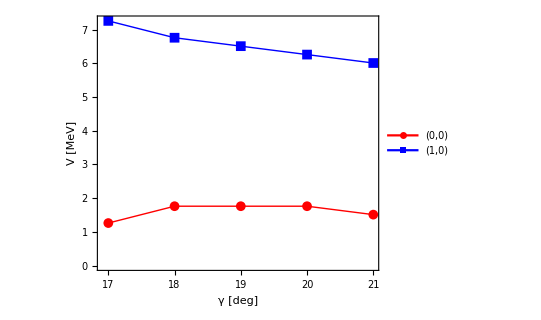

```mathematica
ListPlot[{Table[{gammas[[i]],v00[[i]]},{i,1,Length[gammas]}],Table[{gammas[[i]],v10[[i]]},{i,1,Length[gammas]}]},Joined->True,Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,10},AspectRatio->0.8,FrameLabel->{"γ [deg]","V [MeV]"},PlotLegends->Placed[{"(0,0)","(1,0)"},{0.2,0.4}],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameStyle->Directive[Black,Thick]]
```